## Appendix: Quick reference to Mathematica

### Getting started

```mathematica
Help -> Documentation Center   - Can be used to search for commands of interest

?Command   - gives a fairly detailed description of a command, e.g., ?Plot tells you all about this command.  
	You can use * as a wildcard, for instance ?*Plot* gives a list of all commands with Plot in their name. 
	More help can be found in the menu under "Help", in the Function Navigator or Documentation Center.
	
*   - Times command (2*3 gives 6).  Spaces can also be used but be careful (e.g, a=2 3 gives six
	but a=23 gives twenty-three)

^   - Power command (2^3 gives 8)

n!  - factorial (3! gives 6)

{}  - denotes a list, e.g., {2,3,4}

()  - Places variables together, e.g., (1+x)/(1-x) takes 1+x over 1-x

[]  - Generally used to denote that something is a function of something else

%# - grabs previous output number #.

%  - grabs the previous line of output regardless of the number

%% - grabs output two lines back.  Note: naming outputs is safer (see next section).

f /. object1 -> object2  
           - tells Mathematica to make replace object1 with object2 in the function
          e.g.,  3*x^2 /. x -> 2*y+z gives  3*(2*y + z)^2
```

### Avoiding conflict with Mathematica

Mathematica tends to use capital letters for its functions, so its often a good idea to use 
lower case names for your functions and variables.

If you refer to previous entries using %, it can be difficult to know exactly what your 
previous entry was.  It is safer to assign a name to the output and then refer to this name later.

For example,

```mathematica
myderivative = D[a Sin[b x], x]
```

```mathematica
Plot[myderivative/.a->1/.b->3,{x,0,10}]
```

### Functions and constants in Mathematica (A small fraction!)

Abs[x]  - Takes the absolute value of x

E   - The exponential constant 2.71838.  E^(x) can be invoked using Exp[x]

I   - The square root of negative 1.

Infinity   - Self-explanatory.

Log[x]   -Takes the natural log of x

Log[b,x]   -Takes the log of x in base b

Pi   - 3.14159...

Sin[x], Cos[x], Tan[x]   - trigonometric functions
ArcSin[x], ArcCos[x], ArcTan[x] -  inverse trigonometric functions

Sqrt[x]   - Square root

### Writing equations in Mathematica

```mathematica
x=y   - Sets x to y immediately and from then on (use Clear[x] to unassign x), e.g., plot1=Plot[x^2,{x,0,10}]

x:=y   - Does nothing until x is called, at which point x is assigned the value y

x==y    - Tests whether x equals y BUT makes no assignment

f[x_]:=  - This is how you define a function (called "f") of x, e.g., f[x_] := x^2

f[x] - This gives the function evaluated at x, e.g., f[3] gives 9 in the above example

f[x_,y_,...]=  - This is how you define a function of several variables
```

### A list of helpful commands

Clear[symbol1,symbol2,...] - clears variable or function definitions, 
	e.g., Clear[x, y, pop1]

Clear[“Global`*”] - clears all variable or function definitions from memory

Collect[eqn,{terms},Factor] - collects parts of an equation involving “terms” and 
	factors them separately (if only one “term”, the braces aren’t needed)
	e.g. Collect[a-b+a x-2 b x+a^2 x^2+2 a b x^2+b^2 x^2, x, Factor]

D[f,x]   - takes the partial derivative of f with respect to x - e.g. D[x^2+y Log[x], x]

D[f, {x, n}]   - takes the nth derivative with respect to x - e.g.  D[x^2+y Log[x],{x,2}]

DSolve[eqn, y[x],x]   - solves differential equation for y as a function of x 
	(SYMBOLICALLY) e.g. DSolve[{y'[x] == k y[x], y[0]==y0, y[x],x]

DSolve[eqns, {y1,y2,y3,..}, x] same as above but for a system of eqns 
	e.g. pred-prey equations DSolve[{y'[x] == k y-x, z'[x]==x+z}, {y[x],z[x]}, x]

NDSolve[eqns, y, {x, xmin,xmax}] - same as DSolve but seeks solution
	NUMERICALLY - e.g. NDSolve[{y'[x] ==4 y[x], y[3]==62}, y[x], {x, 0,20}]

Expand[expr]- expands an expr e.g. Expand[(1+x)^2] gives 1+2x+x^2

Evaluate[object] - evaluates a symbolic object like interpolating functions

Factor[polynomial] - self explanatory - e.g. Factor[x^2 + 2 x + 1]

FindRoot[eqn1==eqn2, {x, x0}] - searches for numerical root of eqn1==eqn2
            starting at x0 e.g. FindRoot[Log[x] + x + Arctan[x] == 0, {x, 4}] tries to find 
            x that satisfies this very ugly - impossible to solve by hand equation, starting at x=4.

For[start,test,increment,body] - repeats procedure “body”, starting from “start”  
	until the “test” condition is met, adding “increment” each time, 
	e.g., For[i=1, i≤10, i=i+1, Print[i]] prints out integers 1 through 10.

Integrate[f,x] - finds indefinite integral of f with respect to x 
	e.g., Integrate[Log[x], x]

Integrate[f, {x, xmin, xmax}] - computes definite integral from xmin to xmax
	e.g., Integrate[Log[x], {x, 1,6}]

ListPlot[list] - plots a list of integers, e.g., ListPlot[{2,4,3,5,4}]

ListPlot[{{x1, y1},{x2, y2},...}] - plots a series of {x, y} values,
	e.g., ListPlot[{{1,2},{2,1},{5,7}}] To join the points with a line use:
	 ListPlot[{{1,2},{2,1},{5,7}},PlotJoined->True] (in Mathematica 5)
	 ListPlot[{{1,2},{2,1},{5,7}},Joined->True] (in more recent versions)

N[f] - gives a numerical value for an expression - e.g. N[Pi] gives 3.14159

Part[eqn,i] - grabs  the ith part of eqn, e.g., Part[3x^2+x^3,2] gives x^3

Plot[f,{x,xmin,xmax}] - plots f versus x on the interval [xmin,xmax] 
            e.g., Plot[x^2, {x,0,2}]   NOTE: Plot has lots of options e.g. AxesLabel,
            Grid, AxesOrigin, etc. See the manual for a complete list and usage 
            e.g.,  Plot[x^2, {x,0,2}, PlotStyle->Dashed] makes a dashed curve.

Plot3D[f, {x, xmin, xmax}, {y, ymin, ymax}] - makes a 3D plot of f

Show[graphics, options] - displays graphic objects using options e.g. 
	Show[popplot1, PlotJoined->True]

Simplify[expr] - does its best to simplify an expression, expr

Solve[eqns, vars] - tries to solve one or a system equations for the vars specified 
	(SYMBOLICALLY)- e.g. Solve[{x+y ==1, x-y ==4}, {x,y}]

NSolve[eqns, vars] - does the same thing as  Solve, but does it NUMERICALLY
	(See also FindRoot)

Sum[f, {i, imin, imax}] - sums  f from i to imax i.e. f[1] + f[2] + f[3] + ... 
            (only really interesting if f depends on i) - e.g. Sum[i, {i, 1,4}] gives 10.
            
Reduce[{eqns}] - can be used to determine if a statement is true or false 
	e.g., Reduce[{a + b > 1, a < 0, b < 0}]
	
RSolve[eqns, vars] - solves a discrete-time equation for y as a function of x 
	(SYMBOLICALLY) e.g. RSolve[{n[t+1] == R n[t], n[0]==n0}, n[t],t]
	
Table[f, {i, imin, imax}]- makes a table in list format of the function f
	with i values that run from imin to imax - e.g. Table[i, {i, 1,4}] gives {1,2,3,4}.

### Libraries

Mathematica has some libraries or packages that it does not load automatically.
The Documentation Center will tell you if a function needs a library.
For example, to plot error bars on a list plot, you will need:

```mathematica
Needs["ErrorBarPlots`"]
```

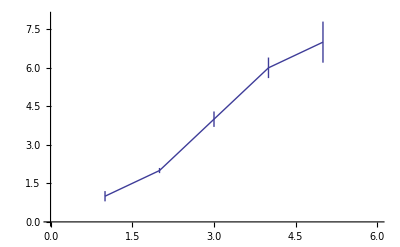

```mathematica
ErrorListPlot[{{{1,1},ErrorBar[0.2]},{{2,2},ErrorBar[0.1]},{{3,4},ErrorBar[0.3]},{{4,6},ErrorBar[0.4]},{{5,7},ErrorBar[0.8]}}, Joined->True,PlotRange->{{0,6},{0,8}}]
```